## Unit Square Graph paper

Fill in myMotief with your drawing.

This makes two images - one with graph paper, one without.
Save the non-graph paper version

Use “Save Selection As” under File to save your image.

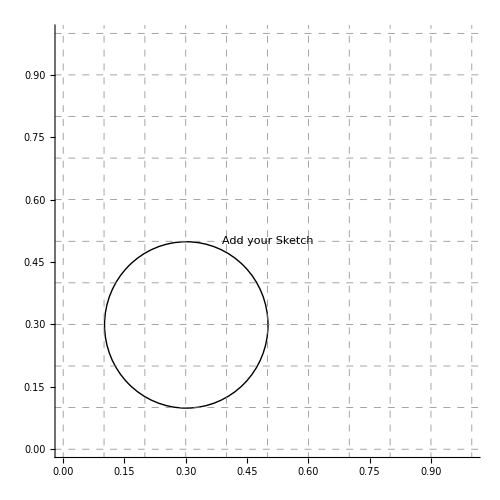

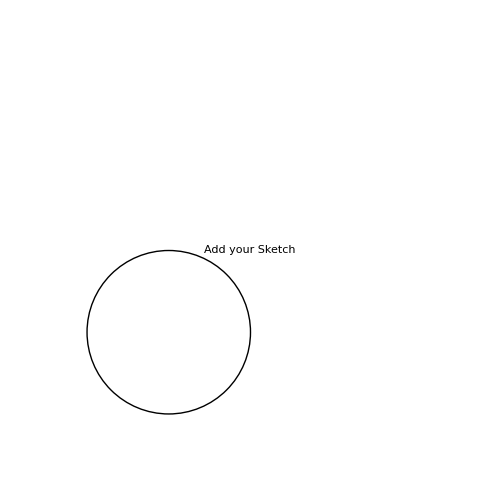

```mathematica
myMotief = {
			(* fill in *) Circle[ {.3,.3}, .2],
			Text["Add your Sketch", {.5,.5}]
		};
Graphics[
		{
			myMotief
	       },

		{
			PlotRange-> { {0,1}, {0,1} },
			AspectRatio -> 1,
			GridLines-> {  Range[0,1, .1], Range[0,1, 0.1] },
			GridLinesStyle -> Directive[ Gray, Dashed ],
			Axes-> True,
			ImageSize-> 500
	      }
		]



Graphics[
		{
			myMotief
	       },

		{
			PlotRange-> { {0,1}, {0,1} },
			AspectRatio -> 1,
			ImageSize-> 500
	      }
		]
```